# GHZ STATES - Noise model of IBMQ_16_melbourne

## N = 2 (depth 6)

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=2;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

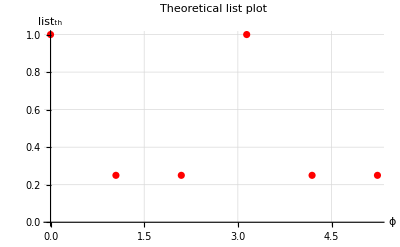

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

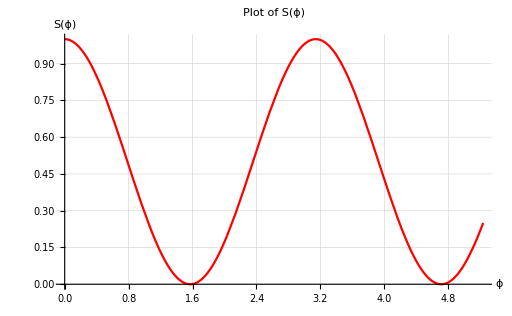

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

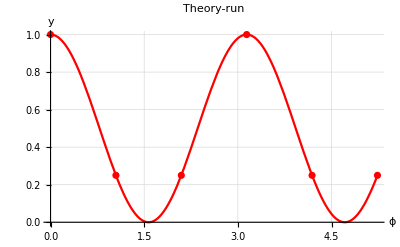

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

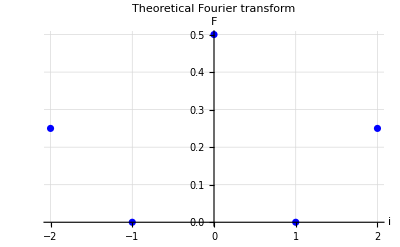

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

RUN

8192 shots

```mathematica
data1={0.8577880859375,0.2669677734375,0.2750244140625,0.861572265625,0.2760009765625,0.2708740234375};
```

#### Plot of the data choosen

```mathematica
run=data1  (*inserire il data che si vuole*)
Length[run]
```

{0.857788,0.266968,0.275024,0.861572,0.276001,0.270874}

6

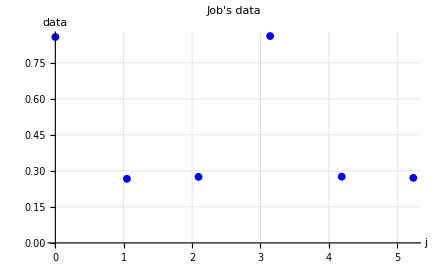

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

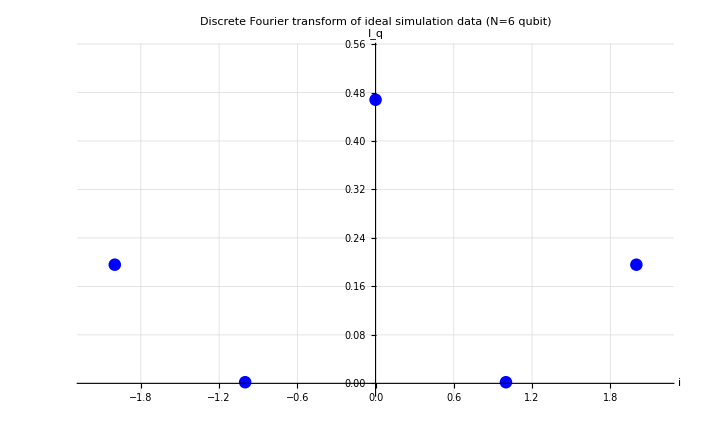

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{Style["i",Black,FontFamily->"HoldForm",FontSize->16],Style["I_q",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Discrete Fourier transform of ideal simulation data (N=6 qubit)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{-0.01,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

Fidelity

```mathematica
F1=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data1[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F2Lower1= 2 √F1[[Length[F1]]]
F2Upper1=√(F1[[n+1]]/2)+√F1[[Length[F1]]]
```

0.885035

0.926272

COMPARE

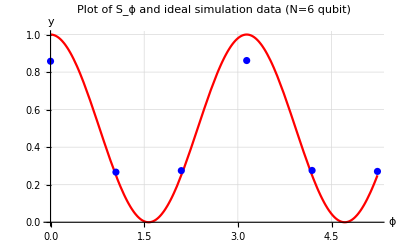

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->
{Style["ϕ",Black,FontFamily->"HoldForm",FontSize->16],Style["y",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Plot of S_ϕ and ideal simulation data (N=6 qubit)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

## N = 3 (depth 8)

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=3;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

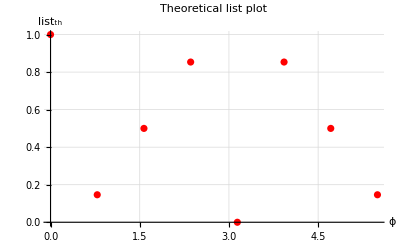

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

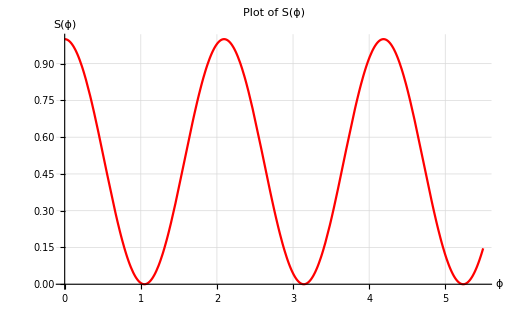

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

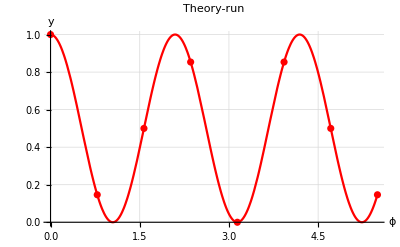

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

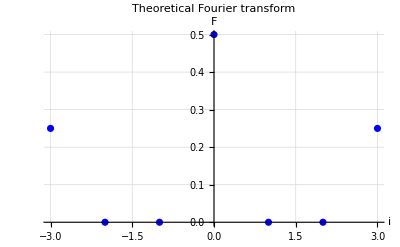

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

RUN

8192 shots

```mathematica
data1={0.734619140625,0.1717529296875,0.4100341796875,0.6500244140625,0.0733642578125,0.650146484375,0.402099609375,0.1717529296875};
```

#### Plot of the data choosen

```mathematica
run=data1  (*inserire il data che si vuole*)
Length[run]
```

{0.734619,0.171753,0.410034,0.650024,0.0733643,0.650146,0.4021,0.171753}

8

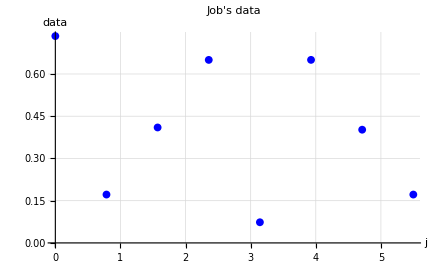

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

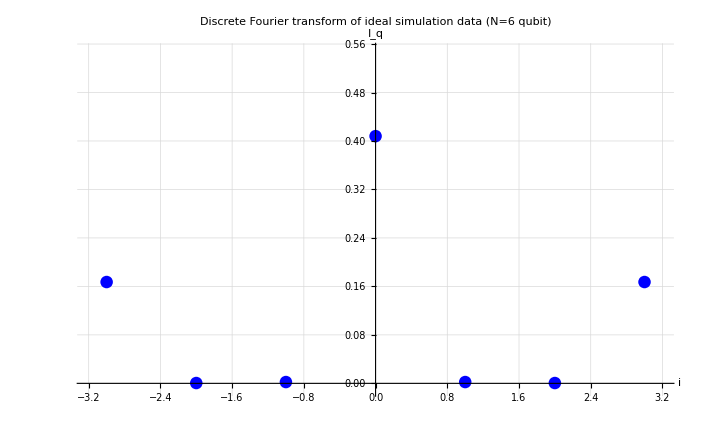

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{Style["i",Black,FontFamily->"HoldForm",FontSize->16],Style["I_q",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Discrete Fourier transform of ideal simulation data (N=6 qubit)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{-0.01,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

Fidelity

```mathematica
F1=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data1[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F3Lower1= 2 √F1[[Length[F1]]]
F3Upper1=√(F1[[n+1]]/2)+√F1[[Length[F1]]]
```

0.817846

0.860572

COMPARE

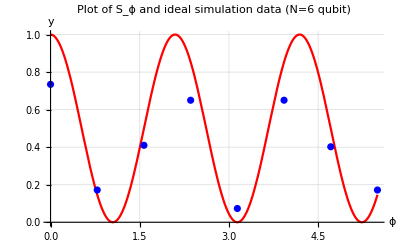

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->
{Style["ϕ",Black,FontFamily->"HoldForm",FontSize->16],Style["y",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Plot of S_ϕ and ideal simulation data (N=6 qubit)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

## N = 4 (depth 10)

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=4;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

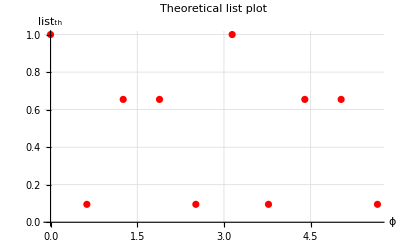

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

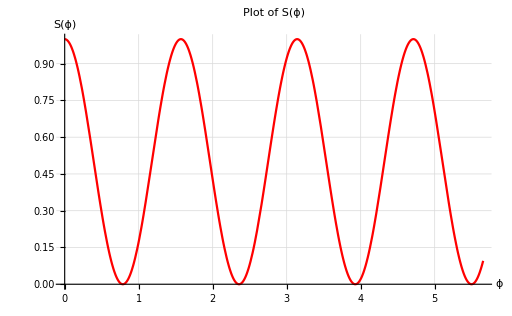

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

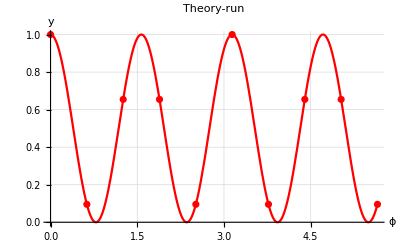

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

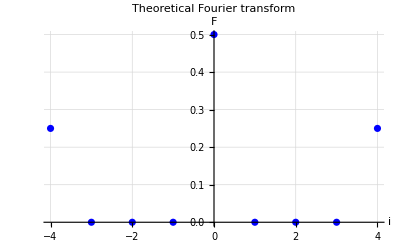

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

RUN

8192 shots

```mathematica
data1={0.6353759765625,0.131591796875,0.440185546875,0.43310546875,0.1302490234375,0.6422119140625,0.12646484375,0.439697265625,0.439453125,0.1343994140625};
```

#### Plot of the data choosen

```mathematica
run=data1  (*inserire il data che si vuole*)
Length[run]
```

{0.635376,0.131592,0.440186,0.433105,0.130249,0.642212,0.126465,0.439697,0.439453,0.134399}

10

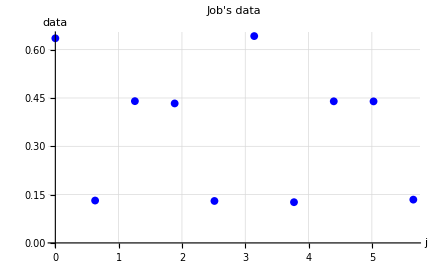

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

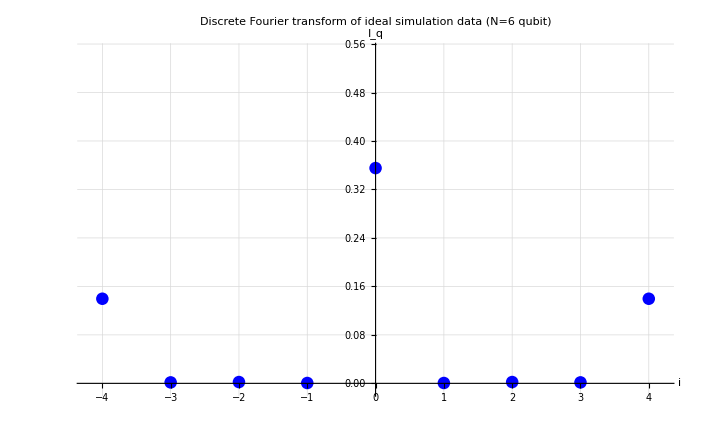

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{Style["i",Black,FontFamily->"HoldForm",FontSize->16],Style["I_q",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Discrete Fourier transform of ideal simulation data (N=6 qubit)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{-0.01,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

Fidelity

```mathematica
F1=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data1[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F4Lower1= 2 √F1[[Length[F1]]]
F4Upper1=√(F1[[n+1]]/2)+√F1[[Length[F1]]]
```

0.747338

0.795139

COMPARE

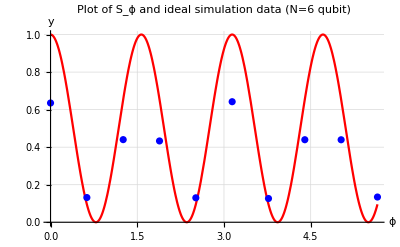

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->
{Style["ϕ",Black,FontFamily->"HoldForm",FontSize->16],Style["y",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Plot of S_ϕ and ideal simulation data (N=6 qubit)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

## N = 5 (depth 12)

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=5;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

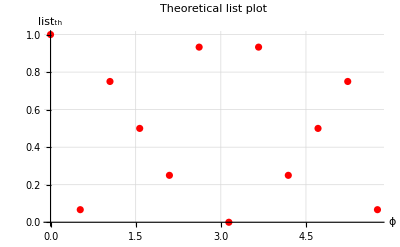

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

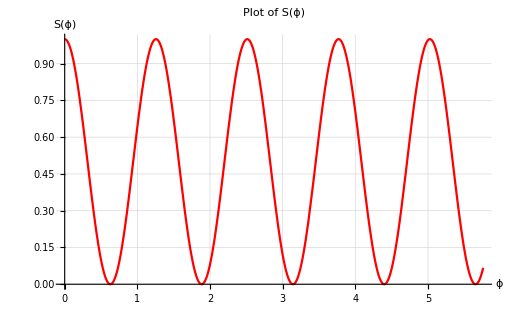

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

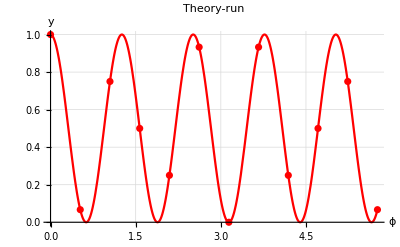

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

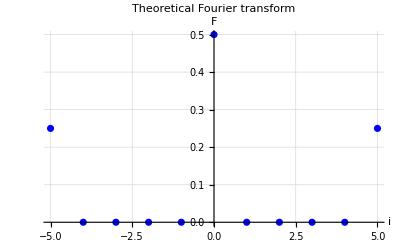

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

RUN

8192 shots

```mathematica
data1={0.544189453125,0.109375,0.4334716796875,0.3236083984375,0.1995849609375,0.5107421875,0.0753173828125,0.514892578125,0.1947021484375,0.3128662109375,0.420654296875,0.11474609375};
```

#### Plot of the data choosen

```mathematica
run=data1  (*inserire il data che si vuole*)
Length[run]
```

{0.544189,0.109375,0.433472,0.323608,0.199585,0.510742,0.0753174,0.514893,0.194702,0.312866,0.420654,0.114746}

12

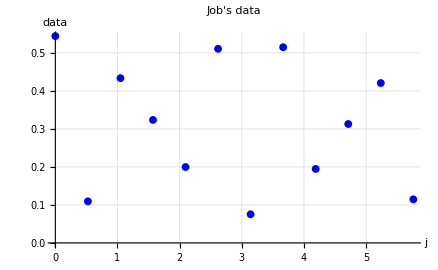

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

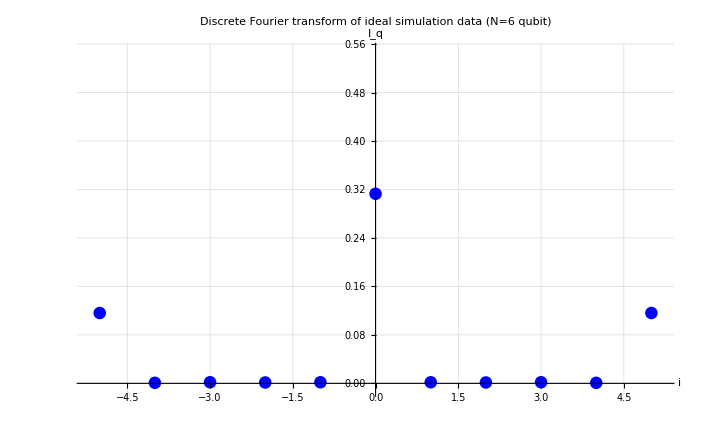

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{Style["i",Black,FontFamily->"HoldForm",FontSize->16],Style["I_q",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Discrete Fourier transform of ideal simulation data (N=6 qubit)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{-0.01,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

Fidelity

```mathematica
F1=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data1[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F5Lower1= 2 √F1[[Length[F1]]]
F5Upper1=√(F1[[n+1]]/2)+√F1[[Length[F1]]]
```

0.681409

0.736208

COMPARE

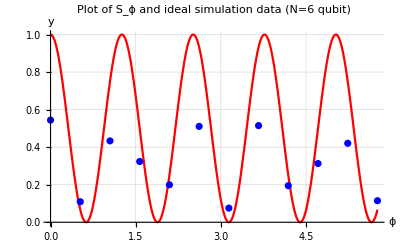

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->
{Style["ϕ",Black,FontFamily->"HoldForm",FontSize->16],Style["y",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Plot of S_ϕ and ideal simulation data (N=6 qubit)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

## N = 6 (depth 14)

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=6;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

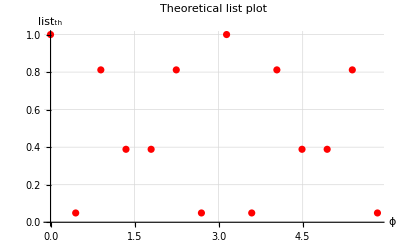

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

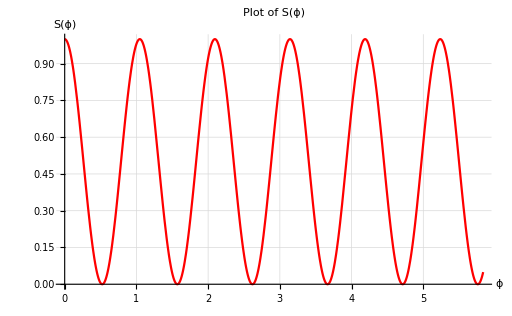

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

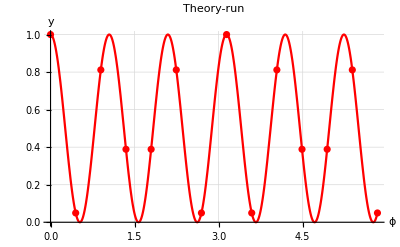

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

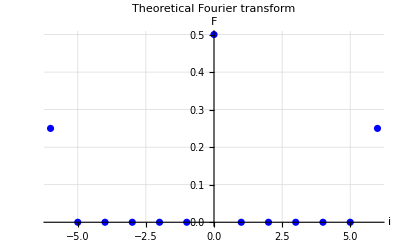

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

RUN

8192 shots

```mathematica
data1={0.4688720703125,0.092529296875,0.391845703125,0.232177734375,0.2293701171875,0.4029541015625,0.09326171875,0.470458984375,0.0955810546875,0.3966064453125,0.2349853515625,0.220947265625,0.3907470703125,0.0870361328125};
```

#### Plot of the data choosen

```mathematica
run=data1  (*inserire il data che si vuole*)
Length[run]
```

{0.468872,0.0925293,0.391846,0.232178,0.22937,0.402954,0.0932617,0.470459,0.0955811,0.396606,0.234985,0.220947,0.390747,0.0870361}

14

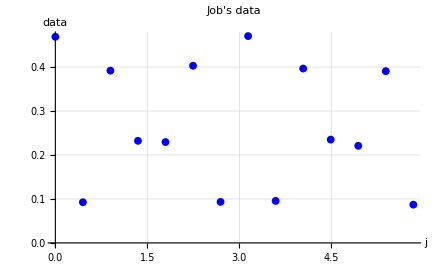

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

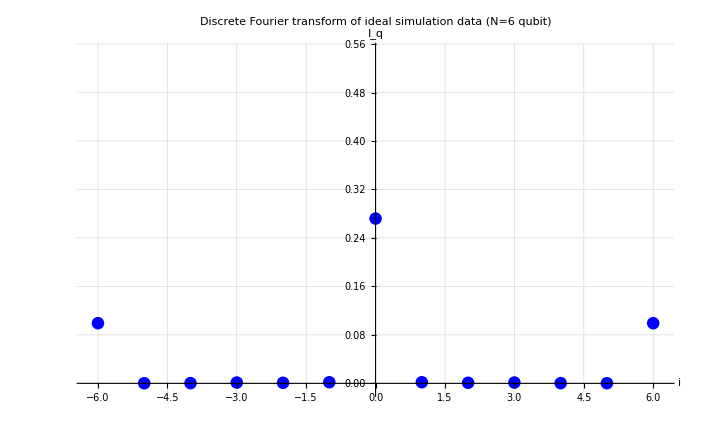

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{Style["i",Black,FontFamily->"HoldForm",FontSize->16],Style["I_q",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Discrete Fourier transform of ideal simulation data (N=6 qubit)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{-0.01,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

Fidelity

```mathematica
F1=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data1[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F6Lower1= 2 √F1[[Length[F1]]]
F6Upper1=√(F1[[n+1]]/2)+√F1[[Length[F1]]]
```

0.630172

0.683838

COMPARE

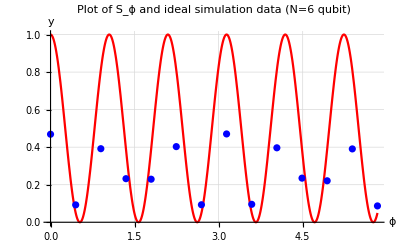

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->
{Style["ϕ",Black,FontFamily->"HoldForm",FontSize->16],Style["y",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Plot of S_ϕ and ideal simulation data (N=6 qubit)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

## N = 7 (depth 16)

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=7;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

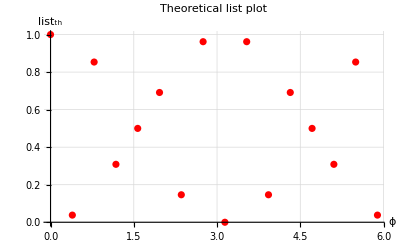

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

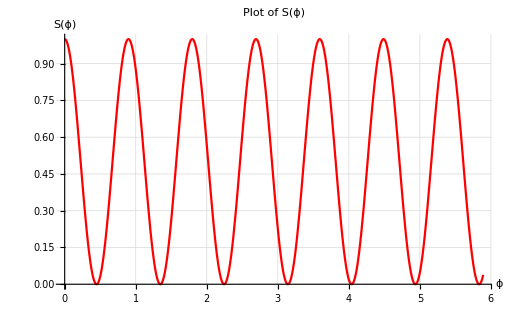

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

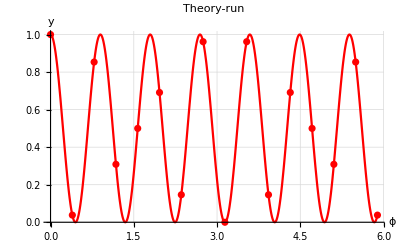

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

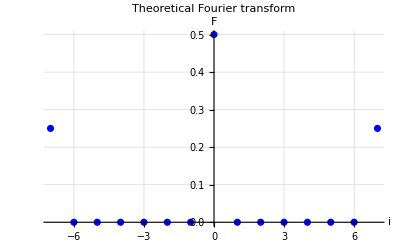

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

RUN

8192 shots

```mathematica
data1={0.42333984375,0.0880126953125,0.3736572265625,0.18359375,0.2529296875,0.313720703125,0.12744140625,0.4039306640625,0.0721435546875,0.4140625,0.115234375,0.322265625,0.247314453125,0.1834716796875,0.3712158203125,0.0867919921875};
```

#### Plot of the data choosen

```mathematica
run=data1  (*inserire il data che si vuole*)
Length[run]
```

{0.42334,0.0880127,0.373657,0.183594,0.25293,0.313721,0.127441,0.403931,0.0721436,0.414063,0.115234,0.322266,0.247314,0.183472,0.371216,0.086792}

16

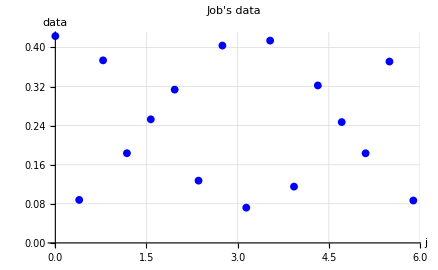

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

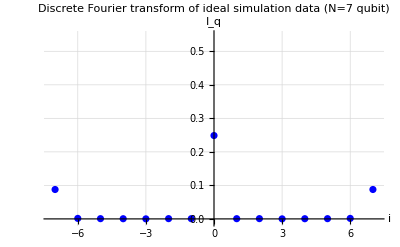

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{Style["i",Black,FontFamily->"HoldForm",FontSize->16],Style["I_q",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Discrete Fourier transform of ideal simulation data (N=7 qubit)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{-0.01,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

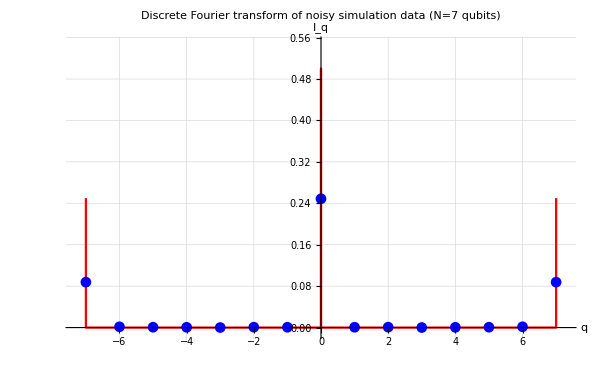

```mathematica
verticalSize=430;
orSize=600;
Fideale=Insert[Insert[Insert[Insert[Subscript[F, th],0,2],0,n+1+1],0,n+1+1+1+1],0,2n+1+1+1+1];
lideale=Insert[Insert[Insert[Insert[l,-n,2],0,n+1+1],0,n+1+1+1+1],n,2n+1+1+1+1];
FPlotideale=ListLinePlot[Thread[{lideale,Fideale}],AxesLabel->{Style["q",Black,FontFamily->"HoldForm",FontSize->16],Style["I_q",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Discrete Fourier transform of ideal simulation data (N=6 qubits)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{-0.01,0.55}}, PlotLegends->{},PlotStyle->{Red}];

Show[FPlotideale,Subscript[FPlot, run],AxesLabel->{Style["q",Black,FontFamily->"HoldForm",FontSize->16],Style["I_q",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Discrete Fourier transform of noisy simulation data (N=7 qubits)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.3,n+0.3},{-0.01,0.55}}, PlotLegends->{},PlotStyle->{Red} ,ImageSize->{orSize,verticalSize}]
```

Fidelity

```mathematica
F1=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data1[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F7Lower1= 2 √F1[[Length[F1]]]
F7Upper1=√(F1[[n+1]]/2)+√F1[[Length[F1]]]
```

0.592391

0.648825

COMPARE

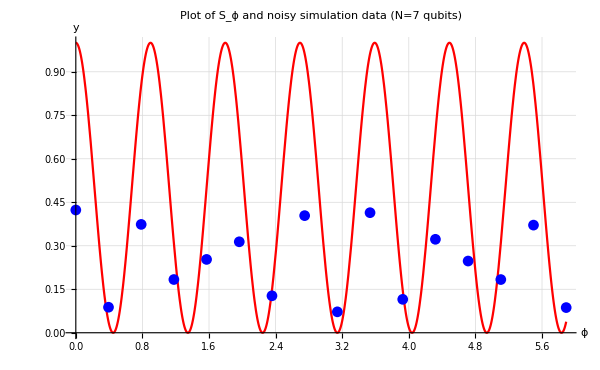

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->
{Style["ϕ",Black,FontFamily->"HoldForm",FontSize->16],Style["y",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Plot of S_ϕ and noisy simulation data (N=7 qubits)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},ImageSize->{orSize,verticalSize}]
```

## N = 8 (depth 18)

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=8;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

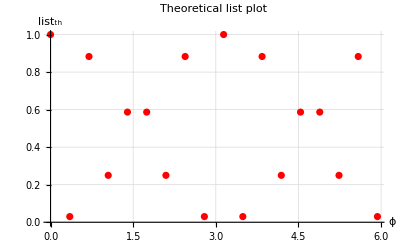

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

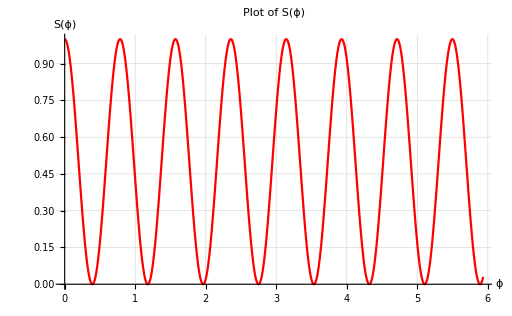

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

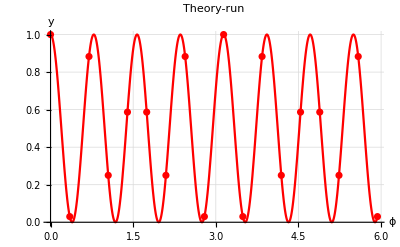

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

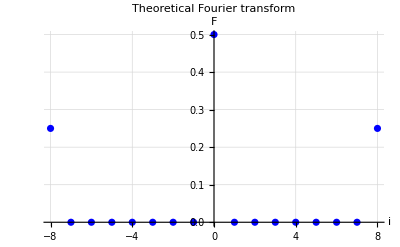

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

RUN

8192 shots

```mathematica
data1={0.2681884765625,0.117431640625,0.246337890625,0.15478515625,0.1865234375,0.197509765625,0.1502685546875,0.241943359375,0.1124267578125,0.26904296875,0.116943359375,0.24462890625,0.15234375,0.195068359375,0.1942138671875,0.1490478515625,0.236328125,0.115234375};
```

#### Plot of the data choosen

```mathematica
run=data1  (*inserire il data che si vuole*)
Length[run]
```

{0.268188,0.117432,0.246338,0.154785,0.186523,0.19751,0.150269,0.241943,0.112427,0.269043,0.116943,0.244629,0.152344,0.195068,0.194214,0.149048,0.236328,0.115234}

18

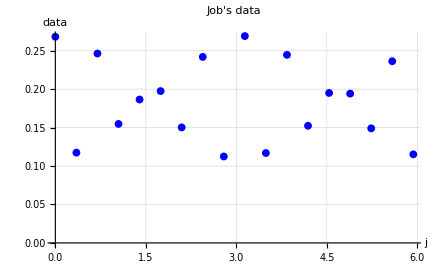

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

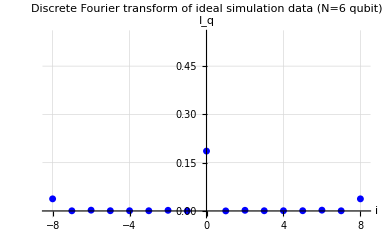

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{Style["i",Black,FontFamily->"HoldForm",FontSize->16],Style["I_q",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Discrete Fourier transform of ideal simulation data (N=6 qubit)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{-0.01,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

Fidelity

```mathematica
F1=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data1[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F8Lower1= 2 √F1[[Length[F1]]]
F8Upper1=√(F1[[n+1]]/2)+√F1[[Length[F1]]]
```

0.387783

0.498862

COMPARE

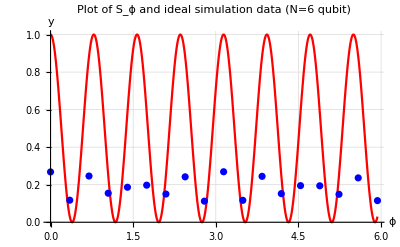

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->
{Style["ϕ",Black,FontFamily->"HoldForm",FontSize->16],Style["y",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Plot of S_ϕ and ideal simulation data (N=6 qubit)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

## N = 9 (depth 20)

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=9;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

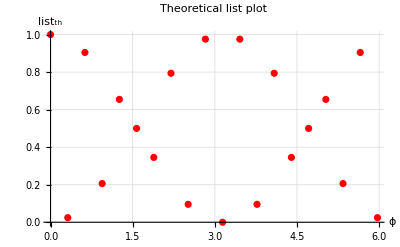

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

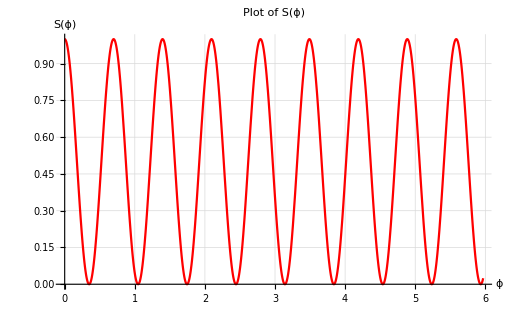

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

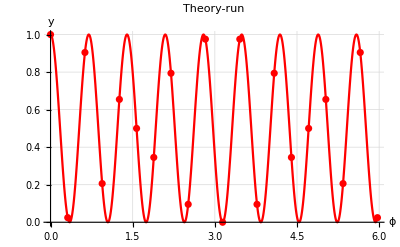

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

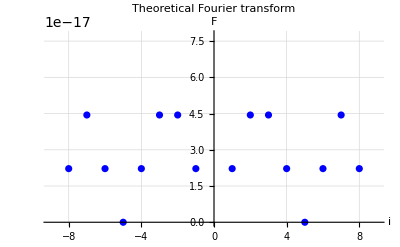

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

RUN

8192 shots

```mathematica
data1={0.2325439453125,0.0894775390625,0.2232666015625,0.1168212890625,0.17626953125,0.1630859375,0.1363525390625,0.2091064453125,0.098388671875,0.2337646484375,0.08837890625,0.2325439453125,0.1026611328125,0.2032470703125,0.139892578125,0.1646728515625,0.1800537109375,0.1177978515625,0.2244873046875,0.086181640625};
```

#### Plot of the data choosen

```mathematica
run=data1  (*inserire il data che si vuole*)
Length[run]
```

{0.232544,0.0894775,0.223267,0.116821,0.17627,0.163086,0.136353,0.209106,0.0983887,0.233765,0.0883789,0.232544,0.102661,0.203247,0.139893,0.164673,0.180054,0.117798,0.224487,0.0861816}

20

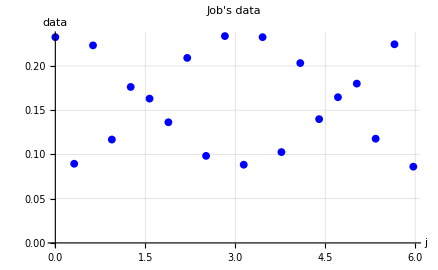

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

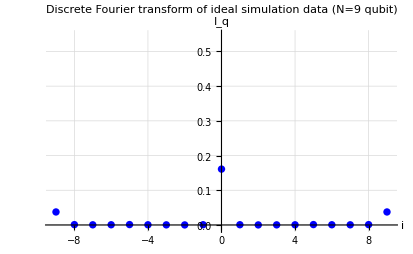

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{Style["i",Black,FontFamily->"HoldForm",FontSize->16],Style["I_q",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Discrete Fourier transform of ideal simulation data (N=9 qubit)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{-0.01,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

Fidelity

```mathematica
F1=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data1[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F9Lower1= 2 √F1[[Length[F1]]]
F9Upper1=√(F1[[n+1]]/2)+√F1[[Length[F1]]]
```

0.387175

0.477268

COMPARE

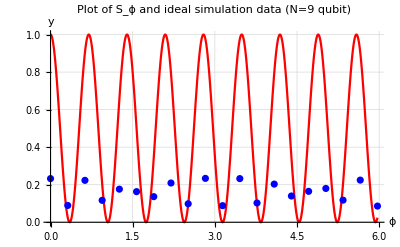

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->
{Style["ϕ",Black,FontFamily->"HoldForm",FontSize->16],Style["y",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Plot of S_ϕ and ideal simulation data (N=9 qubit)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

## Fidelity plot

```mathematica
VLower1={F2Lower1,F3Lower1,F4Lower1,F5Lower1,F6Lower1,F7Lower1,F8Lower1,F9Lower1};
VUpper1={F2Upper1,F3Upper1,F4Upper1,F5Upper1,F6Upper1,F7Upper1,F8Upper1,F9Upper1};
```

```mathematica
qubits={2,3,4,5,6,7,8,9};
```

```mathematica
retta=Plot[0.5,{x,0,9.5},PlotStyle->{Dashing[Tiny],Dashing[Large],Black}];
```

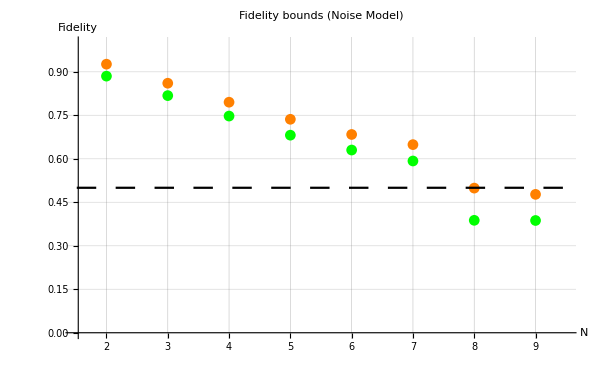

```mathematica
P1L=ListPlot[Thread[{qubits,VLower1}],AxesLabel->{Style["N",Black,FontFamily->"HoldForm",FontSize->16],Style["Fidelity",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Fidelity bounds (Noise Model)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} ,Ticks->{{2,3,4,5,6,7,8,9},Automatic} ,TicksStyle->Medium, GridLines->{{2,3,4,5,6,7,8,9},Automatic} , PlotRange->{{1.5,9.5},{0,1}}, PlotLegends->{},PlotStyle->{Green}];
P1U=ListPlot[Thread[{qubits,VUpper1}],AxesLabel->{Style["N",Black,FontFamily->"HoldForm",FontSize->16],Style["Fidelity",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Fidelity bounds (Noise Model)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->{{2,3,4,5,6,7,8,9},Automatic} ,TicksStyle->Medium, GridLines->{{2,3,4,5,6,7,8,9},Automatic} ,  PlotRange->{{1.5,9.5},{0,1}}, PlotLegends->{},PlotStyle->{Orange}];
a=Show[P1L,P1U,retta,Ticks->{{2,3,4,5,6,7,8,9},Automatic},ImageSize->{orSize,verticalSize}]
```